# The Gauss Seidel Method

In this notebook we will take a look at the Gauss Seidel Method for solving linear systems. Much of this first bit is copied out of our Jacobi Method notebook.

```mathematica
A={{10,-1,2,0},{-1,11,-1,3},{2,-1,10,-1},{0,3,-1,8}};
A//MatrixForm
```

(10 | -1 | 2 | 0
-1 | 11 | -1 | 3
2 | -1 | 10 | -1
0 | 3 | -1 | 8)

We need to divide the Matrix A into the three pieces. It would be nice to have Mathematica do this for us... that sounds like a good homework problem!

```mathematica
Di=DiagonalMatrix[{10,11,10,8}];
Di//MatrixForm
```

(10 | 0 | 0 | 0
0 | 11 | 0 | 0
0 | 0 | 10 | 0
0 | 0 | 0 | 8)

```mathematica
U=-{{0,-1,2,0},{0,0,-1,3},{0,0,0,-1},{0,0,0,0}};
U//MatrixForm
```

(0 | 1 | -2 | 0
0 | 0 | 1 | -3
0 | 0 | 0 | 1
0 | 0 | 0 | 0)

```mathematica
L=-{{0,0,0,0},{-1,0,0,0},{2,-1,0,0},{0,3,-1,0}};
L//MatrixForm
```

(0 | 0 | 0 | 0
1 | 0 | 0 | 0
-2 | 1 | 0 | 0
0 | -3 | 1 | 0)

Let’s just make sure we did it right!

```mathematica
b={6,25,-11,15};
MatrixForm[b]
```

(6
25
-11
15)

```mathematica
Di-L-U-A//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Now we use the matrix T for the Gauss-Seidel Method.

```mathematica
T=Inverse[Di-L].U;
T//MatrixForm
```

(0 | 1/10 | -1/5 | 0
0 | 1/110 | 4/55 | -3/11
0 | -21/1100 | 13/275 | 4/55
0 | -51/8800 | -47/2200 | 49/440)

Here is the vector c for the Gauss-Seidel Method.

```mathematica
c=Inverse[Di-L].b;
c//MatrixForm
```

(3/5
128/55
-543/550
3867/4400)

The iterator has the same form as before.

```mathematica
It[{x_,T_,c_}]:={T.x+c,T,c}
```

```mathematica
N[Nest[It,{{0,0,0,0},T,c},5]][[1]]
```

{1.00009,2.00002,-1.00003,0.999988}

```mathematica
LinearSolve[A,b]
```

{1,2,-1,1}

Now let’s look at the (absolute error) for G-S and Jacobi.

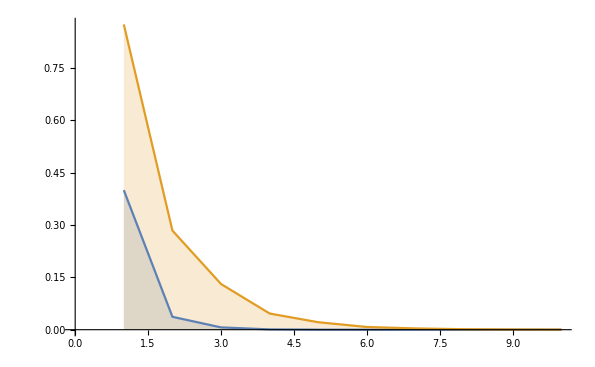

```mathematica
sol=LinearSolve[A,b];
Error[x_,s_]:=Norm[x-s,Infinity]
errors=Table[Error[N[Nest[It,{{0,0,0,0},T,c},i][[1]]],sol],{i,1,10}];
ListLinePlot[{errors,{0.875,0.28409090909090917,0.1308806818181818,0.0463042355371901,0.021350510072314144,0.007758739317242691,0.0035943101506739072,0.0013296988776434482,0.0006191901399694721,0.00023205298996442636}},Filling->Axis,PlotRange->Full]
```

Here we see G-S in blue and Jacobi in orange. The convergence for G-S is noticably better!